```mathematica
filesAR=FileNames["/home/carla/GDC/LYE/GDC_Conf_AR_LYE_DOJ_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/LYE/GDC_Conf_BR_LYE_DOJ_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{0.000138939,5,35987},{0.000138939,5,35987},{0.00492611,1,203},{0.00588235,1,170},{0.00321543,1,311},{0.00215054,1,465},{0.011236,1,89},{1.,1,1}}

{{0.000138939,40,287896},{0.000138939,5,35987},{0.00492611,3,609},{0.00263158,1,380},{0.0004095,14,34188},{0.00215054,1,465},{0.,0,132}}

```mathematica
dojAR=confAR[[All,1]]
dojBR=confBR[[All,1]]
```

{0.000138939,0.000138939,0.00492611,0.00588235,0.00321543,0.00215054,0.011236,1.}

{0.000138939,0.000138939,0.00492611,0.00263158,0.0004095,0.00215054,0.}

```mathematica
sList={1,2,3,4,5,6,7,8};
sList2={1.5,2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&, ran2];
```

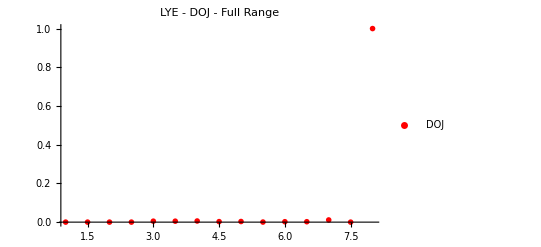

```mathematica
PlotDOJAllParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"LYE - DOJ - Full Range", PlotMarkers->{{"D",12}}]
```

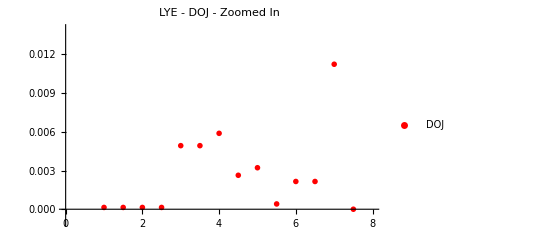

```mathematica
PlotDOJParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->{-0.001, 0.014},  PlotLabel->"LYE - DOJ - Zoomed In",  PlotMarkers->{{"D",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/LYE/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"LYE_DOJ.txt"]
Export["LYE_DOJ.jpeg",PlotDOJAllParts,ImageSize->850]
Export["LYE_DOJ_Zoomed_In.jpeg",PlotDOJParts,ImageSize->850]
```

LYE_DOJ.jpeg

LYE_DOJ_Zoomed_In.jpeg